# The Sandpile Model

Jonas Kaufman & Jon Ueki
May 4, 2016

## The Bak-Tang-Wiesenfeld Model

Cellular automaton to model “spatially extended dynamical systems”

Self-organizing critical behavior with power laws, 1/f noise

Not just sand: earthquakes, human brain, Congress

-Graphics-

http://www.wisegeek.org/what-is-silica-sand.htm

## 1-D Model Rules

Row of N cells representing half a sandpile

Each cell has height h_i and slope z_i where z_i=h_i-h_(i+1)

Adding a grain at cell i:

z_i → z_i+1

z_(i-1) → z_(i-1)-1

If z_i > z_c, cell “topples,” sending one grain of sand to the next cell down:

z_i  → z_i- 2

z_(i±1) → z_(i±1) + 1

Left boundary is closed, right boundary is open

## 1-D Model Rules

-Graphics-

http://link.aps.org/doi/10.1103/PhysRevA.38.364

## 1-D Model in Action

N = 20, z_c=1, z_i=0 initially

Grains added randomly, pile relaxes in between

Reaches stable state z_i = z_c

```mathematica
lbl={FontFamily->"Baskerville",FontSize->20};

length=20;
zCrit1D=1;

constantRow[c_]:=row=Table[c,{length}]

addGrain[] :=Module[{r},
r=RandomInteger[{1,length}];
row[[r]]++;
If[r>1,row[[r-1]]--]
];

relaxation1D[]:=Module[{i,stable=False},
While[!stable,
stable=True;
For[i=1,i≤ length,i++,
If[row[[i]]> zCrit1D,
stable=False;
If[1<i<length,row[[i]]-=2;row[[i+1]]++;row[[i-1]]++;];
If[i==1,row[[i]]-=2;row[[i+1]]++;];
If[i==length,row[[i]]--;row[[i-1]]++];
];
];
];
]

pourSand[numGrains_]:=Module[{n,rows={row}},
For[n=1,n≤numGrains,n++,
addGrain[];
relaxation1D[];
AppendTo[rows,row]; 
];
rows
]

constantRow[0];
rows=pourSand[600];
Animate[GraphicsRow[{
ListStepPlot[rows[[t]],AxesLabel->{"i","z"},Filling->Axis,PlotRange->{-zCrit1D-1,zCrit1D+1},LabelStyle->lbl,ImageSize->Medium],
ListStepPlot[Table[Total[rows[[t]][[i;;]]],{i,length}],AxesLabel->{"i","h"},Filling->Axis,PlotRange->{0,length*zCrit1D+1},LabelStyle->lbl,ImageSize->Medium]
}],
{t,1,Length[rows],1,Appearance->"Labeled"},AnimationRunning->False,AnimationRate->Automatic,AnimationRepetitions->3]
```

## 2-D Model Rules

N x N grid representing a quarter sandpile

“Slope” is z_(i,j)=2 h_(i,j)-h_(i+1,j)-h_(i,j+1)

Adding a grain at z_(i,j):

z_(i,j) → z_(i,j)+2

z_(i-1,j) → z_(i-1,j)-1,  z_(i,j-1) → z_(i,j-1)-1

If z_(i,j) > z_c, cell “topples,” sending one grain down in each direction:

z_(i,j) → z_(i,j)-4

z_(i±1,j) → z_(i±1,j)+1,  z_(i,j±1) → z_(i,j±1)+1

## 2-D Model in Action

N = 20, z_c=2, z_(i,j)=0 initially

```mathematica
gridSize = 20; (* side length of grid *)
zCrit = 2; (* the critical slope *)
constantGrid[c_]:=grid = Table[Table[c, {n, gridSize}], {n, gridSize}]; (* initialize grid to constant slope *)

relaxAll[]:=Module[{i,j,stable=False},
While[!stable,
stable=True;
For[i=1,i≤ gridSize,i++,
For[j=1,j≤ gridSize,j++,
If[grid[[i,j]]> zCrit,
stable=False;
(* remove slope *)
grid[[i,j]]-=2;
If[i≠ gridSize,grid[[i,j]]--];
If[j≠ gridSize,grid[[i,j]]--];
(* add slope to neighbors *)
If[i≠1,grid[[i-1,j]]++];
If[j≠1,grid[[i,j-1]]++];
If[i≠gridSize,grid[[i+1,j]]++];
If[j≠gridSize,grid[[i,j+1]]++];
];
];
];
];
]

update[ii_,jj_]:=Module[{stable=False,look={{ii,jj}},l,i,j},
While[!stable,
stable=True;
For[l=1,l≤ Length[look],l++,
{i,j}=look[[l]];
If[grid[[i,j]]>zCrit,
stable=False;
s++; (* count topple *)
(* remove slope *)
grid[[i,j]]-=2;
If[i≠ gridSize,grid[[i,j]]--];
If[j≠ gridSize,grid[[i,j]]--];
(* add slope to neighbors *)
If[i≠1,grid[[i-1,j]]++];
If[j≠1,grid[[i,j-1]]++];
If[i≠gridSize,grid[[i+1,j]]++];
If[j≠gridSize,grid[[i,j+1]]++];
(* relax neighbors *)
If[i≠1,AppendTo[look,{i-1,j}]];
If[j≠1,AppendTo[look,{i,j-1}]];
If[i≠gridSize,AppendTo[look,{i+1,j}]];
If[j≠gridSize,AppendTo[look,{i,j+1}]];
];
];
T++;
];
]

addGrain[random_,place_] :=Module[{i, j}, 
If[random,(*If we activate random, then add grains randomly*)
i=RandomInteger[{1,gridSize}];j=RandomInteger[{1,gridSize}];,
i=place[[1]];j=place[[2]];
];
grid[[i,j]]+=2;
If[j≠1,grid[[i,j-1]]--];
If[i≠1,grid[[i-1,j]]--];
update[i,j];
]

run[totalSand_, random_:False,place_:{1,1}] := Module[{n,sList={},TList={}},
For[n=1,n≤ totalSand,n++,
s=0;T=0;
addGrain[random,place];
AppendTo[sList,s];AppendTo[TList,T];
];
{grid,sList}
]

heights[grid_]:=Module[{i,j,gridSize=Length[grid],heights},
heights=Table[Table[0, {gridSize}], {gridSize}];
For[i=gridSize-1,i> 0,i--,
For[j=gridSize-1,j> 0,j--,
heights[[i,j]]= 0.5(grid[[i,j]]+heights[[i+1,j]]+heights[[i,j+1]]);
];
];
heights
]

heightsFull[grid_]:=Module[{i,j,h,gridSize=Length[grid],heights},
heights=Table[Table[0, {n, 2*gridSize}], {n, 2*gridSize}];
For[i=gridSize-1,i≥0,i--,
For[j=gridSize-1,j≥0,j--,
h=0.5(If[i==0 || j==0,grid[[i+1,j+1]] ,grid[[i,j]]]
+ heights[[i+1 + gridSize,j + gridSize]]
+heights[[i + gridSize,j+1 + gridSize]]);
heights[[gridSize+i,gridSize+j]]=h;
heights[[gridSize+i, gridSize - j]] =h;
heights[[gridSize-i, gridSize+j]] = h;
heights[[gridSize-i, gridSize - j]] = h;
];
];
heights
]

sDist[sList_]:=Module[{dist=Table[0,{Max[sList]}],s,t},
For[t=1,t≤ Length[sList],t++,
s=sList[[t]];
If[s≠0,
dist[[s]]++
];
];
1./Length[sList] dist
]

hDisp:=ListPlot3D[heightsFull[g0],InterpolationOrder->1, Mesh->None,ColorFunction->"Rainbow",ImageSize->Large]

zComp:=Histogram[{Flatten[g0],Flatten[g1]},Automatic,"Probability",AxesLabel->{"z","D(z)"},ChartLegends->{0,4},LabelStyle->lbl,ImageSize->Large];

sFit[sList_]:= FindFit[sDist[sList][[2;;100]],a x^b,{a,b},x];

avComp :=ListLogLogPlot[{sDist[s0],sDist[s1],Table[1./x,{x,Length[sDist[s1]]}]},AxesLabel->{"s","D(s)"},Joined->{False,False,True},PlotLegends->{0,4,"1/s"},LabelStyle->lbl,ImageSize->Large]

zPltComp:=Grid[{{ArrayPlot[g0,PlotLabel-> "z, 0",ImageSize->Medium,PlotLegends->Automatic,ColorFunction->GrayLevel,LabelStyle->lbl],
ArrayPlot[g1,PlotLabel-> "z, 4",ImageSize->Medium,PlotLegends->Automatic,ColorFunction->GrayLevel,LabelStyle->lbl]}}];

constantGrid[0];

Dynamic[Grid[{{ArrayPlot[grid,PlotLabel-> "z",ImageSize->Medium,PlotLegends->Automatic,ColorFunction->GrayLevel,LabelStyle->lbl],
ArrayPlot[heights[grid],PlotLabel-> "h",ImageSize->Medium,PlotLegends->Automatic,ColorFunction->GrayLevel,LabelStyle->lbl]}}]]
```

```mathematica
{g0,s0}=run[15000, True]; (* randomly drop 10000 grains *)
```

## Pile Visualization

```mathematica
hDisp
```

-Graphics3D-

## Supercritical Initial State

N = 20, z_c=2, z_(i,j)=4 initially

```mathematica
Dynamic[Grid[{{ArrayPlot[grid,PlotLabel-> "z",ImageSize->Medium,PlotLegends->Automatic,ColorFunction->GrayLevel,LabelStyle->lbl],
ArrayPlot[heights[grid],PlotLabel-> "h",ImageSize->Medium,PlotLegends->Automatic,ColorFunction->GrayLevel,LabelStyle->lbl]}}]]
```

```mathematica
constantGrid[4];(* initialize slopes *)
```

```mathematica
relaxAll[];(* relax the pile *)
```

```mathematica
{g1,s1}=run[15000, True]; (* randomly drop 10000 grains *)
```

## Final Slope Distributions

Different initial sandpiles reach roughly the same distribution of slopes

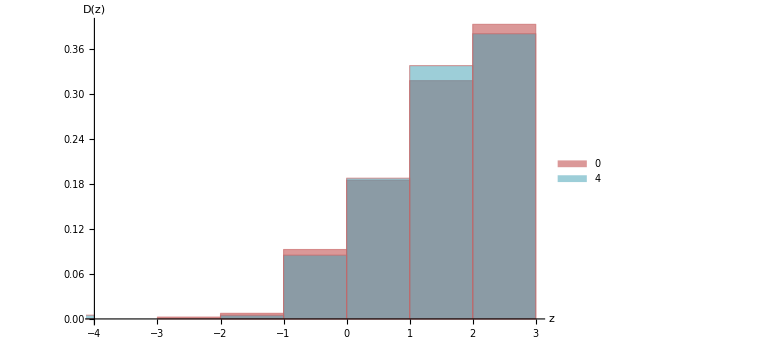

```mathematica
zComp
```

## Avalanche Size Distributions

Critical state displays spatial power law D(s) ≈ ks^-1, in agreement with BTW

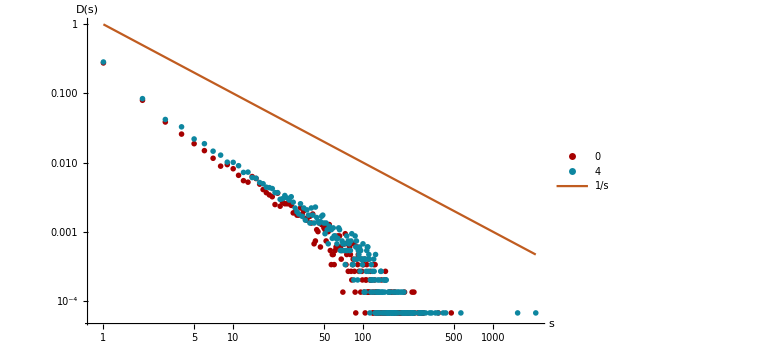

```mathematica
avComp
```

## Conclusions

Model reaches critical state under different initial conditions

Avalanche size distribution roughly follows a power law with power -1

Future directions:

Larger grid, more steps

More detailed avalanche statistics

Different boundary conditions